## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/xelatex","Ghostscript"->"/usr/bin/gs"];
myMaTeX[x_]:= MaTeX[x,"Preamble"->{"\\usepackage{fontspec}","\\setmainfont{DejaVu Serif}"},FontSize->16]
```

```mathematica
myMaTeX2[x_]:= MaTeX[x,FontSize->18]
```

## Load params & Test

```mathematica
particle="JPsi";
centrality="20-40";
```

```mathematica
myParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../input/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&];
myDict=Association[Table[If[StringContainsQ[myParams[[i,2]],","],myParams[[i,1]]->ToExpression/@StringSplit[myParams[[i,2]],","],myParams[[i,1]]->ToExpression[myParams[[i,2]]]],{i,1,Length[myParams]}]]
```

<|A→208,collisionType→0,particleType→1,alphas→0,lambdaQCD→0.308,qhat0→0.075,useCentrality→1,centralityEdges→{0,20,40,60,100},lp→1.5,massp→0.938,rootsnn→5023,Ny→21,Npt→81,y_min→-5.,y_max→5.,ptmin→0.1,ptmax→40.1|>

```mathematica
(* load variables from params file to automate some things below *)
roots = myDict["rootsnn"]
```

5023

```mathematica
roots=5023;
```

```mathematica
M =If[ myDict["particleType"]==0,9.45,3.43](*0 for JPsi and 1 for Upsilon*)
```

3.43

```mathematica
cE = Which[roots==5023,"5.02",roots==8160,"8.16"]
```

5.02

```mathematica
centEdges=myDict["centralityEdges"]
centBins=Transpose[{Drop[centEdges,-1],Drop[centEdges,1]}]
centTags=centBins/. {a_,b_}:>ToString@Row[{a,"-",b}]
```

{0,20,40,60,100}

{{0,20},{20,40},{40,60},{60,100}}

{0-20,20-40,40-60,60-100}

### General functions

```mathematica
Mperp2[pt_] = pt^2+M^2; (* GeV ^2 *)
Mperp[pt_] = Sqrt[Mperp2[pt]]; (* GeV *)
ymaxFunction[pt_] = Log[roots/Mperp[pt]];
ptmaxFunction[y_]=Sqrt[(roots Exp[-y])^2 - M^2];
```

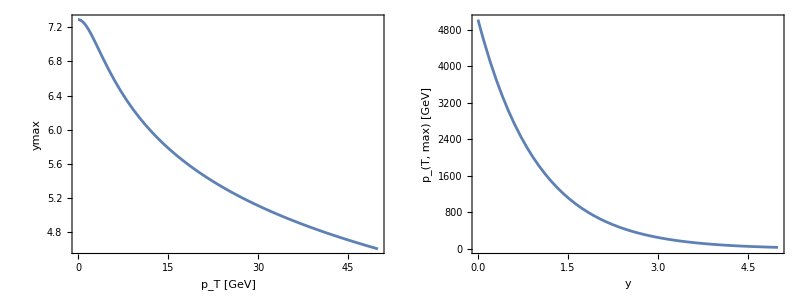

```mathematica
Grid[{{Plot[ymaxFunction[pt],{pt,0,50},FrameLabel->{"p_T [GeV]","ymax"}],Plot[ptmaxFunction[y],{y,0,5},FrameLabel->{"y","p_(T, max) [GeV]"}]}}]
```

## Read & Plot Data

### Read pA data

```mathematica
pAresultLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrorLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pAresult[y_,pt_]:=Exp[pAresultLog[y,pt]]
pAerror[y_,pt_]:=Exp[pAerrorLog[y,pt]]
```

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_pA-cross-section.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_pA-cross-section.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Part::partw: Part 1 of Symbol[] does not exist.

Set::shape: Lists {ymin,ymax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧ are not the same shape.

Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧

Part::partw: Part 2 of Symbol[] does not exist.

Set::shape: Lists {ptmin,ptmax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧ are not the same shape.

Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧

```mathematica
Plot3D[pAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[pAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read AB data

```mathematica
ABresultLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_AB-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
ABerrorLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_AB-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = ABresultLog[[1,1]]
{ptmin,ptmax} = ABresultLog[[1,2]]
ABresult[y_,pt_]:=Exp[ABresultLog[y,pt]]
ABerror[y_,pt_]:=Exp[ABerrorLog[y,pt]]
```

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_AB-cross-section.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_AB-cross-section.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Part::partw: Part 1 of Symbol[] does not exist.

Set::shape: Lists {ymin,ymax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧ are not the same shape.

Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧

Part::partw: Part 2 of Symbol[] does not exist.

Set::shape: Lists {ptmin,ptmax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧ are not the same shape.

Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧

```mathematica
Plot3D[ABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[ABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_pp-cross-section.tsv not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read RAB data

```mathematica
RABresult=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RAB.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RABerror=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RAB.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} = RABresult[[1,1]];
{ptmin,ptmax} =RABresult[[1,2]];
```

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_RAB.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Interpolation[Symbol[],InterpolationOrder→Automatic]

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_RAB.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Interpolation[Symbol[],InterpolationOrder→Automatic]

Part::partw: Part 1 of Symbol[] does not exist.

Set::shape: Lists {ymin,ymax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧ are not the same shape.

Part::partw: Part 2 of Symbol[] does not exist.

Set::shape: Lists {ptmin,ptmax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧ are not the same shape.

```mathematica
Plot3D[RABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RABresultU[y_,pt_]=RABresult[y,pt]+RABerror[y,pt];
RABresultL[y_,pt_]=RABresult[y,pt]-RABerror[y,pt];
```

```mathematica
myPlotY[pt_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_AB"},ImageSize->400,PlotRange->Automatic]
myPlotPT[y_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_AB"},ImageSize->400,PlotRange->Automatic]
```

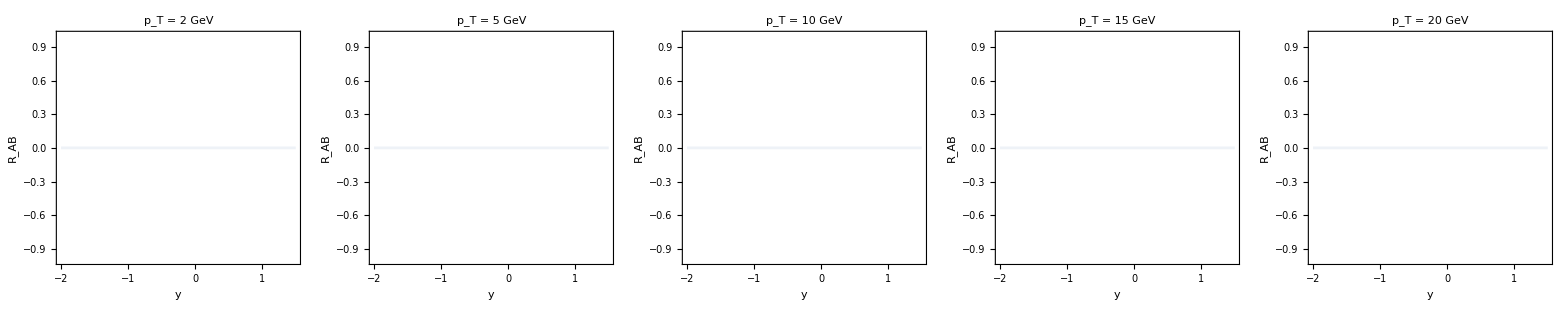

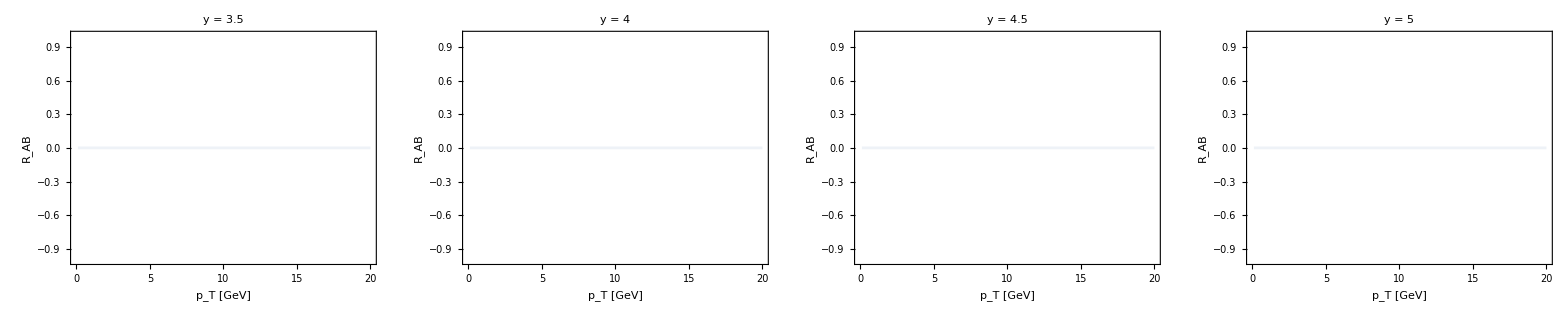

```mathematica
Grid[{{myPlotY[2],myPlotY[5],myPlotY[10],myPlotY[15],myPlotY[20]}}]
Grid[{{myPlotPT[3.5],myPlotPT[4],myPlotPT[4.5],myPlotPT[5]}}]
```

### Read RpA data

```mathematica
RpAresult=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAerror=Interpolation[Import[wd<>"/../output_"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAresult[[1,1]];
{ptmin,ptmax} =RpAresult[[1,2]];
```

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_RpA.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Interpolation[Symbol[],InterpolationOrder→Automatic]

Import::nffil: File /home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/../output_JPsi/cent_20-40_JPsi_RpA.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Interpolation[Symbol[],InterpolationOrder→Automatic]

Part::partw: Part 1 of Symbol[] does not exist.

Set::shape: Lists {ymin,ymax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧ are not the same shape.

Part::partw: Part 2 of Symbol[] does not exist.

Set::shape: Lists {ptmin,ptmax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧ are not the same shape.

```mathematica
mainPlot=Plot3D[RpAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Automatic,PlotRange->{0,5.5}];
(*Plot the plane at z=1*)
planePlot=Plot3D[1,{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Opacity[0.5,Red],Mesh->None];
Show[mainPlot,planePlot]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAresultU[y_,pt_]=RpAresult[y,pt]+RpAerror[y,pt];
RpAresultL[y_,pt_]=RpAresult[y,pt]-RpAerror[y,pt];
```

```mathematica
mypAPlotY[pt_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
mypAPlotPT[y_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
```

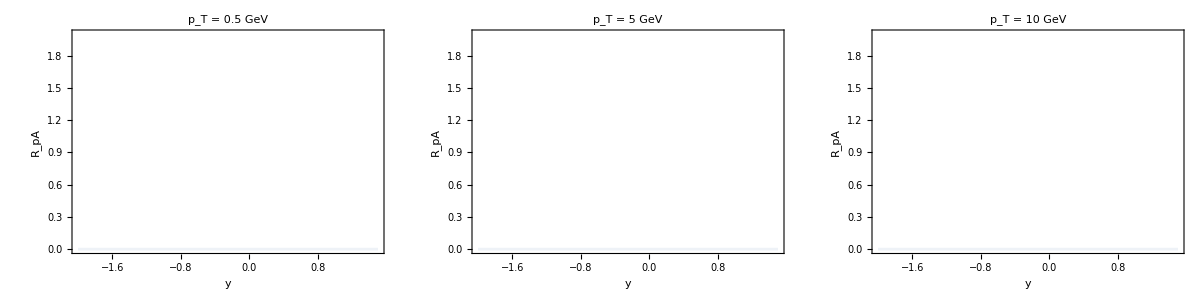

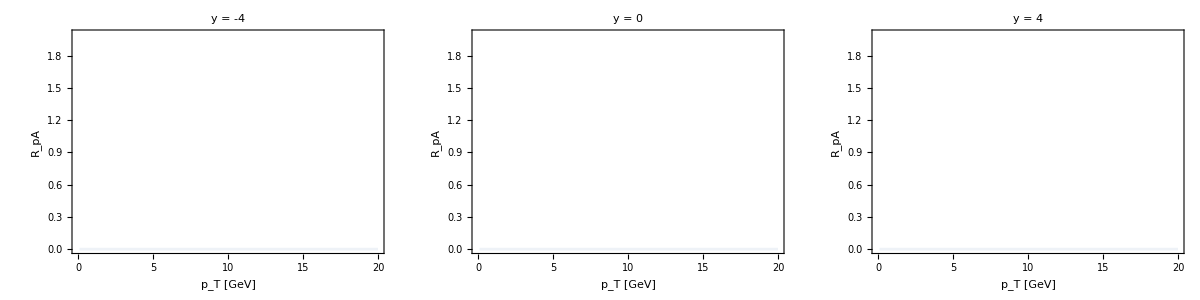

```mathematica
Grid[{{mypAPlotY[0.5],mypAPlotY[5],mypAPlotY[10]}}]
Grid[{{mypAPlotPT[-4],mypAPlotPT[0],mypAPlotPT[4]}}]
```

## RAB vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[RABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,0.0206969},{-4.5,0.0122453},{-4.,0.0101991},{-3.5,0.00926854},{-3.,0.00881111},{-2.5,0.00857266},{-2.,0.00844396},{-1.5,0.0083724},{-1.,0.00833017},{-0.5,0.00830096},{0.,0.00827377},{0.5,0.00823911},{1.,0.00818651},{1.5,0.00810276},{2.,0.00797325},{2.5,0.00778797},{3.,0.0075345},{3.5,0.00719018},{4.,0.0067451},{4.5,0.00626517}}

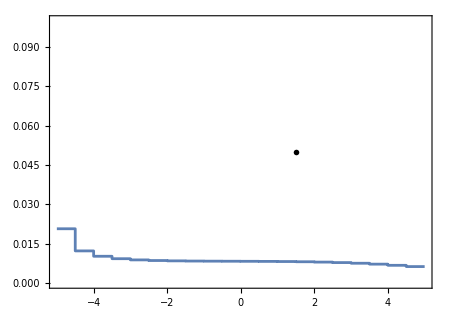

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,0.1}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.05}]}]
```

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.496125,0.590841,0.588272,0.553369,0.517127,0.484471,0.455504,0.429921,0.406751,0.386,0.366694,0.351746,0.33162,0.312788,0.301806,0.277595,0.143005,-0.5481,-2.42279,-6.08992}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.496125},{2.5,0.590841},{5.,0.588272},{7.5,0.553369},{10.,0.517127},{12.5,0.484471},{15.,0.455504},{17.5,0.429921},{20.,0.406751},{22.5,0.386},{25.,0.366694},{27.5,0.351746},{30.,0.33162},{32.5,0.312788},{35.,0.301806},{37.5,0.277595},{40.,0.143005},{42.5,-0.5481},{45.,-2.42279},{47.5,-6.08992}}

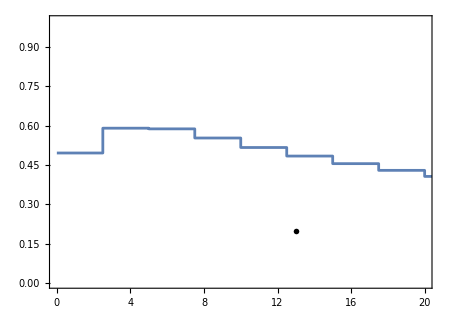

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.468868,0.782578,0.974651,1.11811,1.44557,2.4498,3.62033,2.83917,6.94703,52.1838,5048.96,-8.47711×10^6,-8.10154×10^19,3.19921×10^30,45.0142,379.533,6092.64,34925.9,108463.,247565.}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.468868},{2.5,0.782578},{5.,0.974651},{7.5,1.11811},{10.,1.44557},{12.5,2.4498},{15.,3.62033},{17.5,2.83917},{20.,6.94703},{22.5,52.1838},{25.,5048.96},{27.5,-8.47711×10^6},{30.,-8.10154×10^19},{32.5,3.19921×10^30},{35.,45.0142},{37.5,379.533},{40.,6092.64},{42.5,34925.9},{45.,108463.},{47.5,247565.}}

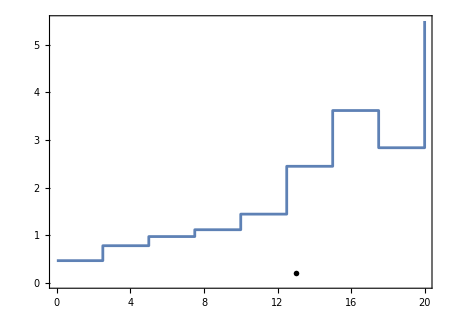

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,5.5}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.485752,0.656832,0.705444,0.699475,0.690295,0.683724,0.680182,0.677554,0.675758,0.674477,0.669507,0.643793,0.604289,0.631549,0.671381,0.671069,0.674839,0.710948,0.819398,1.03901}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.485752},{2.5,0.656832},{5.,0.705444},{7.5,0.699475},{10.,0.690295},{12.5,0.683724},{15.,0.680182},{17.5,0.677554},{20.,0.675758},{22.5,0.674477},{25.,0.669507},{27.5,0.643793},{30.,0.604289},{32.5,0.631549},{35.,0.671381},{37.5,0.671069},{40.,0.674839},{42.5,0.710948},{45.,0.819398},{47.5,1.03901}}

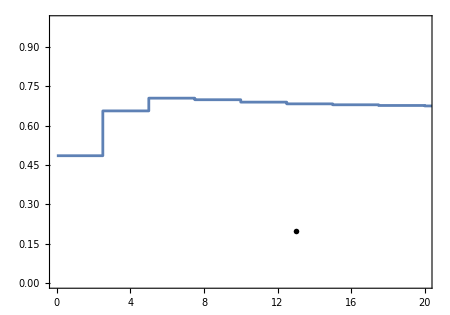

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.48291,0.661395,0.713753,0.708475,0.700052,0.694553,0.69243,0.691339,0.69117,0.691562,0.687869,0.661284,0.619478,0.651295,0.696959,0.698318,0.703,0.73356,0.821668,0.998067}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.48291},{2.5,0.661395},{5.,0.713753},{7.5,0.708475},{10.,0.700052},{12.5,0.694553},{15.,0.69243},{17.5,0.691339},{20.,0.69117},{22.5,0.691562},{25.,0.687869},{27.5,0.661284},{30.,0.619478},{32.5,0.651295},{35.,0.696959},{37.5,0.698318},{40.,0.703},{42.5,0.73356},{45.,0.821668},{47.5,0.998067}}

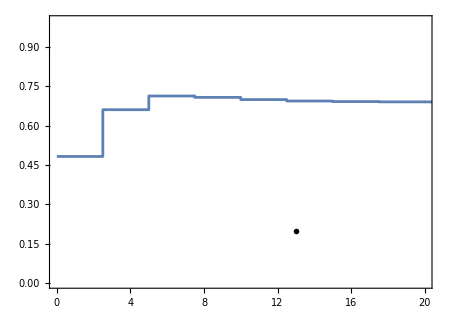

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

## RpA vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,1.04867},{-4.5,0.943557},{-4.,0.895768},{-3.5,0.87083},{-3.,0.85843},{-2.5,0.853237},{-2.,0.851296},{-1.5,0.85021},{-1.,0.849265},{-0.5,0.848321},{0.,0.847334},{0.5,0.846323},{1.,0.845392},{1.5,0.844811},{2.,0.845232},{2.5,0.848218},{3.,0.85756},{3.5,0.883069},{4.,0.951707},{4.5,1.17485}}

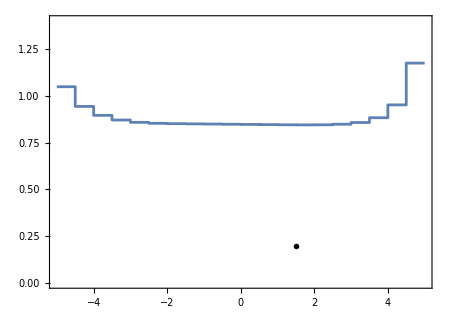

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.2}]}]
```

```mathematica
RpAresultPTavg[{-5,5}]
```

0.890704

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.610284,1.0292,1.15046,1.1009,1.0527,1.02191,1.00267,0.990214,0.981767,0.975762,0.970942,0.967258,0.964486,0.962502,0.963108,0.963035,0.962367,0.963195,0.967735,0.978209}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.610284},{2.5,1.0292},{5.,1.15046},{7.5,1.1009},{10.,1.0527},{12.5,1.02191},{15.,1.00267},{17.5,0.990214},{20.,0.981767},{22.5,0.975762},{25.,0.970942},{27.5,0.967258},{30.,0.964486},{32.5,0.962502},{35.,0.963108},{37.5,0.963035},{40.,0.962367},{42.5,0.963195},{45.,0.967735},{47.5,0.978209}}

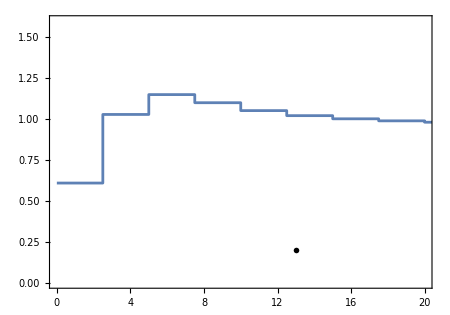

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.6}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.726581,0.971431,1.05357,1.06052,1.06124,1.06797,1.08804,1.14842,1.47178,4.9315,165.341,93639.5,-6.4056×10^16,2.92687×10^27,2.0015,5.43267,28.1743,122.831,358.789,805.749}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.726581},{2.5,0.971431},{5.,1.05357},{7.5,1.06052},{10.,1.06124},{12.5,1.06797},{15.,1.08804},{17.5,1.14842},{20.,1.47178},{22.5,4.9315},{25.,165.341},{27.5,93639.5},{30.,-6.4056×10^16},{32.5,2.92687×10^27},{35.,2.0015},{37.5,5.43267},{40.,28.1743},{42.5,122.831},{45.,358.789},{47.5,805.749}}

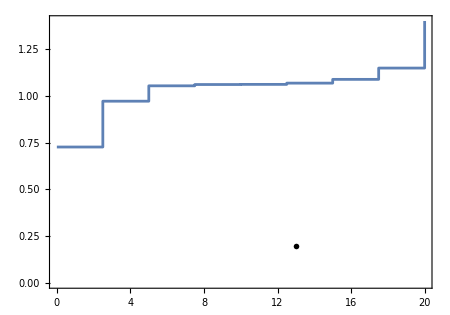

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.701403,0.949515,1.02149,1.01502,1.00391,0.997055,0.99325,0.991183,0.990175,0.989742,0.989622,0.989686,0.989858,0.990114,0.990401,0.990696,0.991012,0.991427,0.992041,0.992953}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.701403},{2.5,0.949515},{5.,1.02149},{7.5,1.01502},{10.,1.00391},{12.5,0.997055},{15.,0.99325},{17.5,0.991183},{20.,0.990175},{22.5,0.989742},{25.,0.989622},{27.5,0.989686},{30.,0.989858},{32.5,0.990114},{35.,0.990401},{37.5,0.990696},{40.,0.991012},{42.5,0.991427},{45.,0.992041},{47.5,0.992953}}

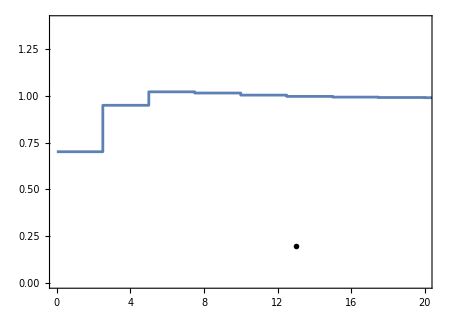

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.707854,0.945658,1.01461,1.0104,1.00129,0.995702,0.992697,0.991148,0.990498,0.990321,0.990387,0.990592,0.990873,0.991217,0.991578,0.991932,0.9923,0.992764,0.993425,0.994384}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.707854},{2.5,0.945658},{5.,1.01461},{7.5,1.0104},{10.,1.00129},{12.5,0.995702},{15.,0.992697},{17.5,0.991148},{20.,0.990498},{22.5,0.990321},{25.,0.990387},{27.5,0.990592},{30.,0.990873},{32.5,0.991217},{35.,0.991578},{37.5,0.991932},{40.,0.9923},{42.5,0.992764},{45.,0.993425},{47.5,0.994384}}

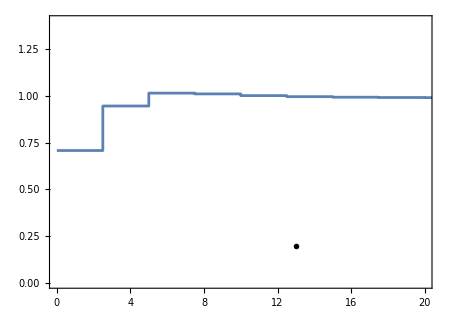

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```